In this project, we explored how partial derivatives fit curves to a set of lines through calculus and graphing. Our project was divided into two main parts. In the first part, we had to formulate a function of two variables that allowed an “n” amount of lines to be plotted onto one graph; this function was based off of the general function of a line, y=mx+b. For the second part of the project, we used partial derivatives with respect to “n” to find the equation of the curve that the lines created.

To begin with, in order to create a function of two variables that have varying values of n, we first had to recognize that each line that creates a curve is a straight line with a y-intercept of n and an x-intercept of (16-n).  Luckily, these two points can be easily used in the slope-intercept form of a line where the slope is -n/(16-n) and the y-intercept is n. After placing this in slope-intercept form, we get the equation below.

```mathematica
f[x_,n_]:=-n/(16-n)*x+n
```

We then used the Table function in Mathematica in order to get all of the different slope-intercept equations for values of n from n=1 to n=15.  Using ContourPlot, we were able to graph all of these lines onto one plot. The only addition we needed to include in the ContourPlot versus the Table was to set all of the equations equal to y, or f(x). Looking at the curve, we predicted that the shape is a quarter of a circle that is centered at (16,16) with a radius of 16.  We guessed this because the curve created has symmetry at the line y=x, which suggests the curve makes a perfect circular path.

```mathematica
Table[f[x,n],{n,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}}]
```

{1-x/15,2-x/7,3-(3 x)/13,4-x/3,5-(5 x)/11,6-(3 x)/5,7-(7 x)/9,8-x,9-(9 x)/7,10-(5 x)/3,11-(11 x)/5,12-3 x,13-(13 x)/3,14-7 x,15-15 x}

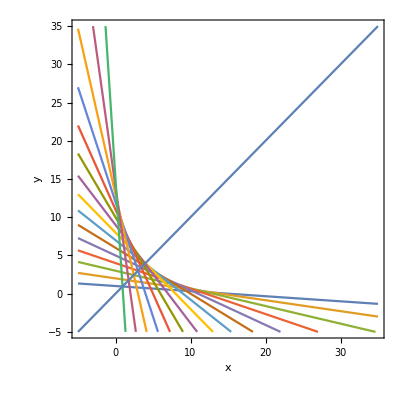

```mathematica
P=ContourPlot[{y==1-x/15,y==2-x/7,y==3-(3 x)/13,y==4-x/3,y==5-(5 x)/11,y==6-(3 x)/5,y==7-(7 x)/9,y==8-x,y==9-(9 x)/7,y==10-(5 x)/3,y==11-(11 x)/5,y==12-3 x,y==13-(13 x)/3,y==14-7 x,y==15-15 x,y==x},{x,-5,35},{y,-5,35},Axes->True,AxesLabel->{x,y},PlotRange->All]
```

Our next step was to find the equation of the curve produced by the graph of all our lines ranging from n=1 to n=15. We looked to optimize the variable of greatest change, n, so we took the partial derivative of our original function f[x,n] with respect to n.

```mathematica
D[f[x,n],n]
```

1-x/(16-n)-(n x)/(16-n)^2

We then set the partial derivative, still with two variables, equal to zero and solved for n so that we could acquire the equations for the values of n when the change in n is equal to zero.

```mathematica
Solve[1-x/(16-n)-(n x)/(16-n)^2==0,n]
```

{{n→-4 (-4+√x)},{n→4 (4+√x)}}

Next, we took these new equations in terms of x: n=-4(-4+√x) and n=4(4+√x) and input them into our original equation, f[x_,n_]:=-n/(16-n)*x+n, in the place of n. The output of the new equations f[x,16+4 √x] and f[x,16-4 √x] yielded the following equations, representative of the desired curve, y=(4+√x)^2 and y=(-4+√x)^2, respectively.

```mathematica
Simplify[f[x,(16+4 √x)]]
```

(4+√x)^2

```mathematica
Simplify[f[x,(16-4 √x)]]
```

(-4+√x)^2

We then graphed these lines together to get an idea of their shape while extending the range of the ContourPlot to better discern. As a side note, the curve that is produced is a parabola that instead of facing upward or downward, is facing upward toward the first quadrant with symmetry at the line y=x as shown in red on the following contour plot.

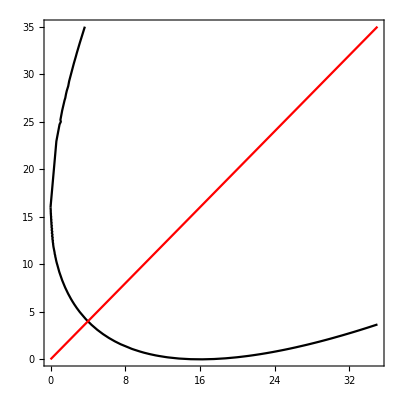

```mathematica
Show[R=ContourPlot[{y==(-4+√x)^2,y==(4+√x)^2},{x,0,35},{y,0,35},ContourStyle->Black],ContourPlot[{y==x},{x,0,35},{y,0,35},ContourStyle->Red]]
```

Next, we added the curve to our original function to see how our derived equations correlated.

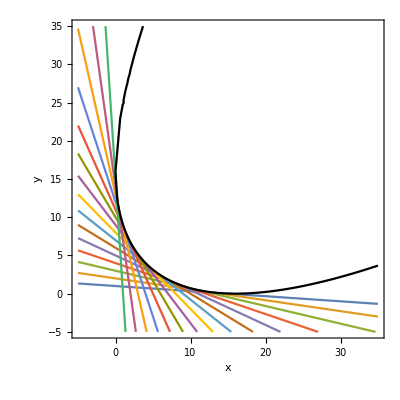

```mathematica
Show[P,R]
```

In order to further explore the process that produced the equations for the shape of the curve, we created a similar function to our original, but this time with the x-intercept as 50-n. We plotted the resulting lines from n=1 to n=49, performed the appropriate partial derivative with respect to n, set the result of the partial derivative equal to zero, solved for n, and then input the two equations back into our original function in the place of n. The resulting lines were graphed with the original equation in order to see how the lines fit the curve.

```mathematica
f[x_,n_]:=-n/(50-n)*x+n
```

```mathematica
Table[f[x,n],{n,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49}}]
```

{1-x/49,2-x/24,3-(3 x)/47,4-(2 x)/23,5-x/9,6-(3 x)/22,7-(7 x)/43,8-(4 x)/21,9-(9 x)/41,10-x/4,11-(11 x)/39,12-(6 x)/19,13-(13 x)/37,14-(7 x)/18,15-(3 x)/7,16-(8 x)/17,17-(17 x)/33,18-(9 x)/16,19-(19 x)/31,20-(2 x)/3,21-(21 x)/29,22-(11 x)/14,23-(23 x)/27,24-(12 x)/13,25-x,26-(13 x)/12,27-(27 x)/23,28-(14 x)/11,29-(29 x)/21,30-(3 x)/2,31-(31 x)/19,32-(16 x)/9,33-(33 x)/17,34-(17 x)/8,35-(7 x)/3,36-(18 x)/7,37-(37 x)/13,38-(19 x)/6,39-(39 x)/11,40-4 x,41-(41 x)/9,42-(21 x)/4,43-(43 x)/7,44-(22 x)/3,45-9 x,46-(23 x)/2,47-(47 x)/3,48-24 x,49-49 x}

```mathematica
A=ContourPlot[{y==1-x/49,y==2-x/24,y==3-(3 x)/47,y==4-(2 x)/23,y==5-x/9,y==6-(3 x)/22,y==7-(7 x)/43,y==8-(4 x)/21,y==9-(9 x)/41,y==10-x/4,y==11-(11 x)/39,y==12-(6 x)/19,y==13-(13 x)/37,y==14-(7 x)/18,y==15-(3 x)/7,y==16-(8 x)/17,y==17-(17 x)/33,y==18-(9 x)/16,y==19-(19 x)/31,y==20-(2 x)/3,y==21-(21 x)/29,y==22-(11 x)/14,y==23-(23 x)/27,y==24-(12 x)/13,y==25-x,y==26-(13 x)/12,y==27-(27 x)/23,y==28-(14 x)/11,y==29-(29 x)/21,y==30-(3 x)/2,y==31-(31 x)/19,y==32-(16 x)/9,y==33-(33 x)/17,y==34-(17 x)/8,y==35-(7 x)/3,y==36-(18 x)/7,y==37-(37 x)/13,y==38-(19 x)/6,y==39-(39 x)/11,y==40-4 x,y==41-(41 x)/9,y==42-(21 x)/4,y==43-(43 x)/7,y==44-(22 x)/3,y==45-9 x,y==46-(23 x)/2,y==47-(47 x)/3,y==48-24 x,y==49-49 x},{x,-5,100},{y,-5,100}];
```

```mathematica
B=ContourPlot[{y==1-x/15,y==2-x/7,y==3-(3 x)/13,y==4-x/3,y==5-(5 x)/11,y==6-(3 x)/5,y==7-(7 x)/9,y==8-x,y==9-(9 x)/7,y==10-(5 x)/3,y==11-(11 x)/5,y==12-3 x,y==13-(13 x)/3,y==14-7 x,y==15-15 x,y==(-4+√x)^2,y==(4+√x)^2},{x,-5,100},{y,-5,100},ContourStyle->Black];
```

```mathematica
D[-n/(50-n)*x+n,n]
```

1-x/(50-n)-(n x)/(50-n)^2

```mathematica
Solve[1-x/(50-n)-(n x)/(50-n)^2==0,n]
```

{{n→-5 (-10+√2 √x)},{n→5 (10+√2 √x)}}

```mathematica
Simplify[f[x,5 (10+√2 √x)]]
```

(5 (10+√2 √x) (34+5 √2 √x+x))/(34+5 √2 √x)

```mathematica
Simplify[5 (10+√2 √x)-(5 (10+√2 √x) x)/(50-5 (10+√2 √x))]
```

50+10 √2 √x+x

```mathematica
Simplify[f[x,(-5 (-10+√2 √x))]]
```

-(5 (-10+√2 √x) (-34+5 √2 √x-x))/(-34+5 √2 √x)

```mathematica
Simplify[-5 (-10+√2 √x)+(5 (-10+√2 √x) x)/(50+5 (-10+√2 √x))]
```

50-10 √2 √x+x

```mathematica
G=ContourPlot[{y==50+10 √2 √x+x,y==50-10 √2 √x+x},{x,-5,100},{y,-5,100},ContourStyle->Gray];
```

As shown in the contour plot below, the black web of lines and the black, narrow parabola represent the function with 15 lines, while the colored web of lines and the gray, wider parabola represent the function with 49 lines. After plotting the first function with the function of n-values, we determined that the number of straight lines used to create this optical illusion-curve affects how wide or steep the parabola is. The greater number of lines, the wider the parabola. The number of lines and x-intercept also affect the vertex of the parabola. The larger the x-intercept and the more lines used increases the vertex in both the positive x and positive y-direction.

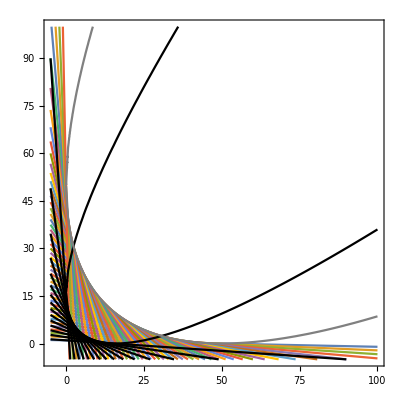

```mathematica
Show[A,B,G]
```

In conclusion, the resulting shape that the straight lines created was a parabola in the first quadrant fixated on the line y=x. Our earlier guess was a quarter of a circle, but we found that this could not be true because we could see as we zoomed out that the shape resembled a parabola rather than a quarter of a circle. Another way we proved that the shape could not be a parabola was to look how the shape changed as the number of lines increased. Only the shape of a parabola would fit this criteria.